```mathematica
{1, 3, 4}
```

{1,3,4}

```mathematica
mylist={1,33,33}
```

{1,33,33}

```mathematica
mylist + 1
```

{2,34,34}

```mathematica
Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Range[3,8]
```

{3,4,5,6,7,8}

```mathematica
mylist[[3]]
```

33

```mathematica
mylist[[1]]
```

```mathematica
1+1
```

2

```mathematica
mylist[[0]]
```

List

```mathematica
Table[i, (i,1,8)]
```

```mathematica
Table[i, {i,1,8}]
```

{1,2,3,4,5,6,7,8}

```mathematica
Table[i, {i, 1, 8, 2}]
```

{1,3,5,7}

```mathematica
Table[i, {i, 1, 8, 0.2}]
```

{1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.}

```mathematica
RandomInteger[{1,6}]
```

6

```mathematica
dicerolls = RandomInteger[{1,6}, 10]
```

{5,2,4,5,2,3,1,4,5,5}

```mathematica
Mean[dicerolls]
```

18/5

```mathematica
1.0 * Mean[dicerolls]
```

3.6

```mathematica
dicerolls = RandomInteger[{1,6}, 10000000];
```

```mathematica
1.0 * Mean[dicerolls]
```

3.5003

```mathematica
squares = Table[i^2, {i, 1, 8}]
```

{1,4,9,16,25,36,49,64}

```mathematica
upto8 = Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Map[f, {a, b, c}]
```

{f[a],f[b],f[c]}

```mathematica
Map[#^2 &, upto8]
```

{1,4,9,16,25,36,49,64}

```mathematica
Map[Sqrt[#] &, squares]
```

{1,2,3,4,5,6,7,8}

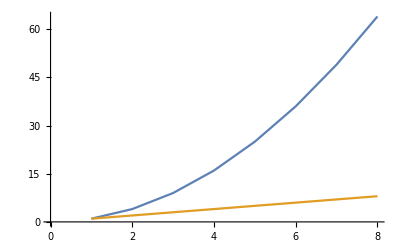

```mathematica
ListPlot[{squares, upto8}, Joined->True]
```

```mathematica
Length[upto8]
```

8

```mathematica
NestList[f, a, 5]
```

{a,f[a],f[f[a]],f[f[f[a]]],f[f[f[f[a]]]],f[f[f[f[f[a]]]]]}

```mathematica
NestList[#+1 &, 1, 5]
```

{1,2,3,4,5,6}

```mathematica
NestList[#*2&,1,5]
```

{1,2,4,8,16,32}

```mathematica
NestWhileList[#*2&,1,#≤129&]
```

{1,2,4,8,16,32,64,128,256}

```mathematica
{1,2,3} + {a,b,c}
```

{1+a,2+b,3+c}

```mathematica
Union[{1,2,3},{3,4}]
```

{1,2,3,4}

```mathematica
Intersection[{1,2,3,4}, {3,4,5}]
```

{3,4}

```mathematica
Join[{1,2,3},{3,4,5}]
```

{1,2,3,3,4,5}

```mathematica
Riffle[{1,2},{a,b}]
```

{1,a,2,b}

```mathematica
Take[Range[10],3]
```

{1,2,3}

```mathematica
Drop[Range[10],3]
```

{4,5,6,7,8,9,10}

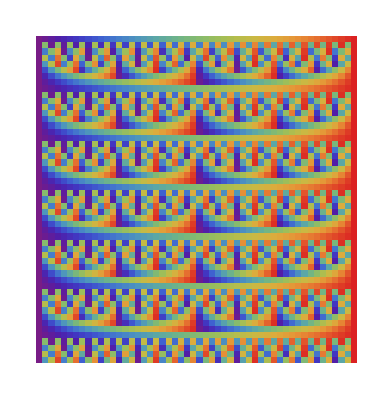

```mathematica
ArrayPlot[NestList[Riffle[Take[#,26], Drop[#,26]] &, Range[52], 52], ColorFunction->"Rainbow"]
```

```mathematica
MatrixForm[{{1,2}, {3,4}}]
```

(1 | 2
3 | 4)

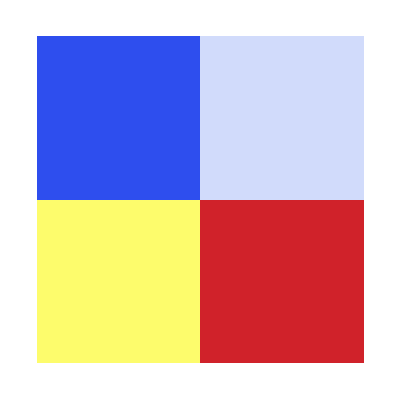

```mathematica
ArrayPlot[{{1,2}, {3,4}}, ColorFunction->"TemperatureMap"]
```

```mathematica
Sqrt[4]
```

2

```mathematica
timestwoadd[x_] := 2*x+1
```

```mathematica
timestwoadd[1]
```

3

```mathematica
timestwoadd[4]
```

9

```mathematica
fn := #*2+1&
```

```mathematica
fn[4]
```

9

```mathematica
testifinputis7 [x_] := If[x == 7, 1, 0]
```

```mathematica
testifinputis7[1]
```

0

```mathematica
testifinputis7[7]
```

1

```mathematica
Map[testifinputis7, Range[9]]
```

{0,0,0,0,0,0,1,0,0}

```mathematica
If[4>2, 1, 0]
```

1

```mathematica
Map[{#, Mod[#,5]}&, Range[30]]
```

{{1,1},{2,2},{3,3},{4,4},{5,0},{6,1},{7,2},{8,3},{9,4},{10,0},{11,1},{12,2},{13,3},{14,4},{15,0},{16,1},{17,2},{18,3},{19,4},{20,0},{21,1},{22,2},{23,3},{24,4},{25,0},{26,1},{27,2},{28,3},{29,4},{30,0}}

```mathematica
collatz[x_, y_] := If[x==3*y || x==2*y+1||y==3*x|| y==2*x+1, 1, 0]
```

```mathematica
Array[#^2&,10]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Array[#^2&, {4,2}]
```

{{1,1},{4,4},{9,9},{16,16}}

```mathematica
Array[#1+2*#2&, {4,4}]
```

{{3,5,7,9},{4,6,8,10},{5,7,9,11},{6,8,10,12}}

```mathematica
MatrixForm[Array[#1+2#2&, {4,4}]]
```

(3 | 5 | 7 | 9
4 | 6 | 8 | 10
5 | 7 | 9 | 11
6 | 8 | 10 | 12)

```mathematica
Array[collatz[#1,#2]&, {20,20}]
```

{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
AdjacencyGraph[Array[collatz[#1,#2]&, {50,50}]]
```

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
GraphPlot3D[AdjacencyGraph[Array[collatz[#1,#2]&, {150,150}]]]
```

-Graphics3D-

```mathematica
Map[Mod[#,7]&, Range[10]]
```

{1,2,3,4,5,6,0,1,2,3}

```mathematica
Position[Map[Mod[#,7]&, Range[100]], 6]
```

{{6},{13},{20},{27},{34},{41},{48},{55},{62},{69},{76},{83},{90},{97}}

```mathematica
Array[{1,2,3}, {2,2}]
```

{{{1,2,3}[1,1],{1,2,3}[1,2]},{{1,2,3}[2,1],{1,2,3}[2,2]}}

```mathematica
{{1,2,3}, {55,66}}
```

{{1,2,3},{55,66}}

```mathematica
Flatten[{{1,2,3}, {55,66}}]
```

```mathematica
{1,2,3,55,66}
```

{1,2,3,55,66}

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Select[Table[i,{i,1,10}], Mod[#,3]==0&]
```

{3,6,9}

```mathematica
RandomReal[{0,1},7]
```

{0.370191,0.770834,0.927359,0.645013,0.932937,0.652839,0.54069}

```mathematica
Sort[RandomReal[{0,1},7], #1 ≥ #2&]
```

{0.794928,0.771297,0.72274,0.660421,0.392199,0.315136,0.0463935}